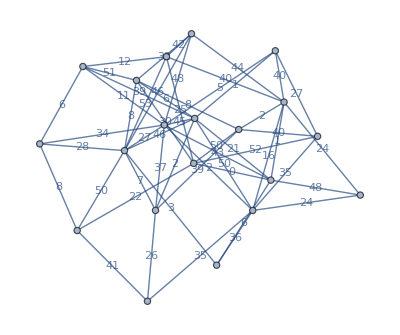

```mathematica
g=Graph[RandomGraph[{20,54}],EdgeCost->RandomInteger[{-54,54},54],EdgeWeight->RandomInteger[54,54],EdgeLabels->"EdgeWeight"]
```

```mathematica
FindMinimumCostFlow[g,1,3]
```

2

```mathematica
EvenMixedGraphAlgorithm[g_?MixedGraphQ]:=Block[{arcs,edges},arcs=EdgeList[g,_->_];edges=EdgeList[g,_<->_];]
```

```mathematica
EdgeList[g],RandomInteger[EdgeCount[g]]
```

{12<->16,7<->18,10<->14,7<->13,2<->14,19<->20,7<->16,1<->3,6<->18,6<->19}

```mathematica
?"*Replace*"
```

```mathematica
DirectedEdge[a<->b]
```

DirectedEdge[a<->b]

```mathematica
First[a<->b]
```

a

```mathematica
EdgeList[g]/.BlockRandom@RandomChoice[{a_<->b_:>a->b,a_<->b_:>a<->b}]
```

{1<->3,1<->11,2<->6,2<->11,2<->13,2<->14,2<->15,2<->16,3<->4,3<->5,3<->6,3<->16,4<->13,4<->14,5<->6,5<->9,5<->16,5<->17,6<->11,6<->16,6<->18,6<->19,6<->20,7<->8,7<->11,7<->13,7<->16,7<->18,7<->19,8<->18,8<->20,9<->11,9<->12,9<->13,9<->14,9<->15,9<->16,10<->14,10<->15,11<->15,11<->17,11<->20,12<->13,12<->15,12<->16,13<->16,13<->17,13<->19,13<->20,14<->15,15<->19,16<->17,17<->20,19<->20}

```mathematica
MapAt[(First[#]->Last[#])&,EdgeList[g],RandomInteger[{1,54},4]]
```

MapAt::partw: Part {31,24,10,43} of {1<->3,1<->11,2<->6,2<->11,2<->13,2<->14,2<->15,2<->16,3<->4,3<->5,«44»} does not exist.

MapAt[First[#1]->Last[#1]&,{1<->3,1<->11,2<->6,2<->11,2<->13,2<->14,2<->15,2<->16,3<->4,3<->5,3<->6,3<->16,4<->13,4<->14,5<->6,5<->9,5<->16,5<->17,6<->11,6<->16,6<->18,6<->19,6<->20,7<->8,7<->11,7<->13,7<->16,7<->18,7<->19,8<->18,8<->20,9<->11,9<->12,9<->13,9<->14,9<->15,9<->16,10<->14,10<->15,11<->15,11<->17,11<->20,12<->13,12<->15,12<->16,13<->16,13<->17,13<->19,13<->20,14<->15,15<->19,16<->17,17<->20,19<->20},{31,24,10,43}]

```mathematica
MapAt[(First[#]->Last[#])&,{a<->b,b<->c,c<->d,d<->a},List/@BlockRandom[RandomInteger[{2,3},2]]]
```

{a<->b,b->c,c<->d,d<->a}

I was trying to create a replace edges in graph function but couldn’t figure it out. I was also trying to create a replace in a random place but couldn’t figure it out either.

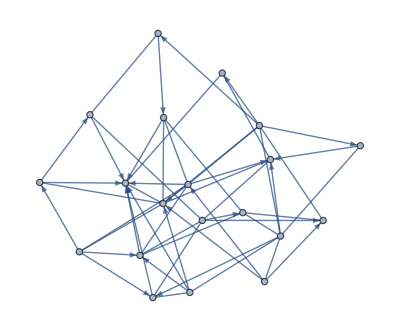

```mathematica
Graph@ReplaceAt[EdgeList[g],x_:>(First[x]->Last[x]),List/@RandomSample[Range@EdgeCount[g],27]]
```

```mathematica
specialembeddings=#<>"Embedding"&/@{"Bipartite","Circular","CircularMultipartite","DiscreteSpiral","Grid","Linear","Multipartite","Spiral","Star"};
```

```mathematica
structuredembeddings=#<>"Embedding"&/@{"Balloon","Radial","LayeredDigraph","Layered"};
```

```mathematica
optimizingembeddings=#<>"Embedding"&/@{"Gravity","HighDimensional","Planar","Spectral","Spherical","SpringElectrical","Spring","Tutte"};
```

```mathematica
graphembeddings=Flatten[{specialembeddings,structuredembeddings,optimizingembeddings}];
```

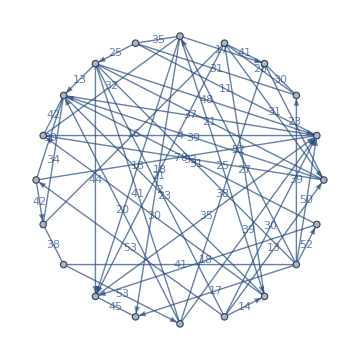
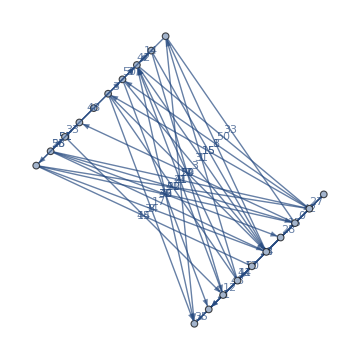
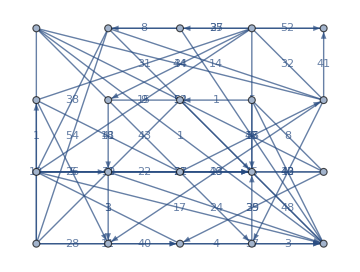
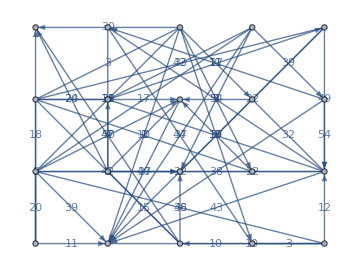
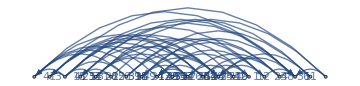
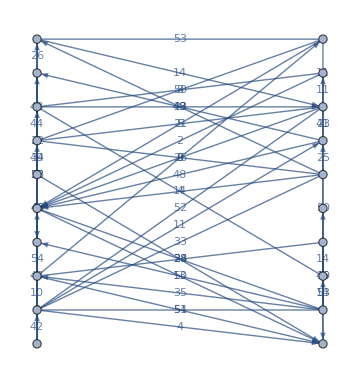
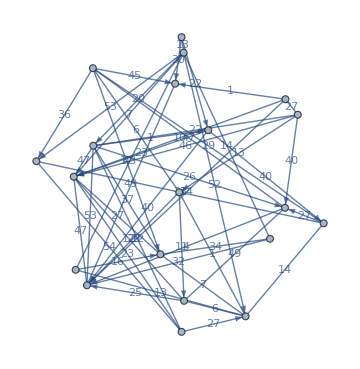
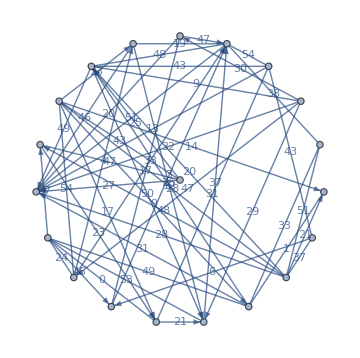

```mathematica
Graph[ReplaceAt[EdgeList[g],x_:>(First[x]->Last[x]),List/@RandomSample[Range@EdgeCount[g],27]],GraphLayout->#,EdgeWeight->RandomInteger[54,54],EdgeLabels->"EdgeWeight",ImageSize->Medium]&/@graphembeddings
```

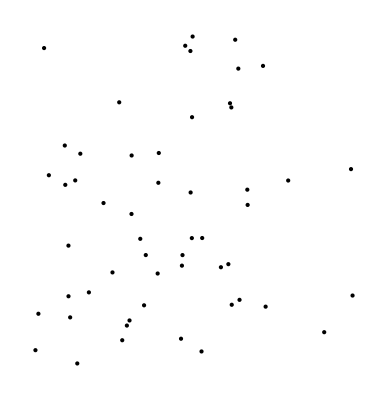

```mathematica
Graphics[Point@RandomPoint[Rectangle[{0,0},{20,20}],54]]
```

```mathematica
points=RandomPoint[Rectangle[{0,0},{20,20}],54]
```

{{17.6647,7.64676},{6.09097,10.1186},{8.6487,18.9197},{5.65971,18.641},{13.8322,12.2297},{15.8121,19.637},{2.30334,14.2538},{5.8598,6.36289},{8.45253,7.69844},{8.29064,12.03},{8.48785,7.3682},{14.0159,17.1232},{5.22403,9.6166},{15.0013,8.65067},{16.9324,7.79078},{3.5548,1.69398},{2.87122,0.155712},{0.688262,0.852099},{12.3955,17.4096},{0.203359,12.545},{3.86037,17.9369},{7.2969,13.3663},{17.5081,19.1008},{10.9098,11.3592},{17.0757,2.54315},{7.36498,16.6267},{17.8157,15.5448},{19.4799,9.98541},{17.8477,3.18781},{0.443176,16.7394},{5.74882,3.07568},{16.0237,18.1146},{10.5089,9.93099},{2.06086,4.41464},{19.4153,16.972},{11.474,16.4762},{12.0592,7.9111},{4.11464,4.09339},{13.2703,1.22539},{17.1468,17.0586},{19.799,12.9715},{10.5155,14.1105},{12.3381,11.699},{4.24721,8.52174},{4.45287,2.49065},{9.22285,7.15102},{7.08948,12.7369},{5.51228,0.474122},{17.6455,9.16901},{13.3714,19.0477},{8.9714,19.9487},{0.799153,16.0245},{3.2431,8.89804},{8.76347,6.59718}}

```mathematica
Nearest[Complement[points,{First[points]}],First[points],5]
```

{{16.9324,7.79078},{17.6455,9.16901},{15.0013,8.65067},{19.4799,9.98541},{17.8477,3.18781}}

```mathematica
EuclideanDistance[#,First[points]]&/@Nearest[Complement[points,{First[points]}],First[points],5]
```

{0.746399,1.52237,2.84634,2.96042,4.4627}

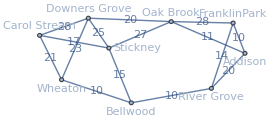
```mathematica
g=-Graphics-;
```

```mathematica
GeoGraphPlot[g]
```

-Graphics-

Compute and plot the most cost effective way of connecting all the cities:

```mathematica
fibernetwork=FindSpanningTree[g];
```

```mathematica
GeoGraphPlot[fibernetwork]
```

-Graphics-

```mathematica
GeoGraphValuePlot[{{Here,Interpreter["StreetAddress"]["1450 Huntington, West Virginia 25701"],GeoDistance[Here,Interpreter["StreetAddress"]["1450 Huntington, West Virginia 25701"]]}}]
```

-Graphics-

```mathematica
TravelDirections[{Interpreter["StreetAddress"]["1234 Charleston Avenue Huntington, WV 25701"],Interpreter["StreetAddress"]["1200 Huntington, WV"]},"Dataset"]
```

```mathematica
TravelDirections[{Interpreter["StreetAddress"]["1234 Charleston Avenue Huntington, WV 25701"],Interpreter["StreetAddress"]["1200 Huntington, WV"]},"TravelPath"]
```

GeoPath[GeoPosition[…],TravelPath]

```mathematica
TravelDirections[{Interpreter["StreetAddress"]["1234 Charleston Avenue Huntington, WV 25701"],Interpreter["StreetAddress"]["1200 Huntington, WV"]},"ManeuverGrid"]
```

Continue onto Charleston Avenue | 0.302 km
Turn right onto 12th Street | 0.533 km
Turn left onto 8th Avenue | 0.615 km
Turn right onto 8th Street, WV 527 | 0.507 km
Arrive at destination |

```mathematica
GeoElevationData[Here,"Orthometric"]
```

174. m

```mathematica
GeoElevationData[GeoPosition[{38.4116094,-82.4345433}],"Orthometric"]
```

174. m

```mathematica
cities={Entity["City",{"Rome","Lazio","Italy"}]<->Entity["City",{"Milan","Lombardy","Italy"}],Entity["City",{"Milan","Lombardy","Italy"}]<->Entity["City",{"Paris","IleDeFrance","France"}],Entity["City",{"Milan","Lombardy","Italy"}]<->Entity["City",{"Frankfurt","Hesse","Germany"}],Entity["City",{"Paris","IleDeFrance","France"}]<->Entity["City",{"Frankfurt","Hesse","Germany"}],Entity["City",{"Paris","IleDeFrance","France"}]<->Entity["City",{"Madrid","Madrid","Spain"}],Entity["City",{"Paris","IleDeFrance","France"}]<->Entity["City",{"London","GreaterLondon","UnitedKingdom"}],Entity["City",{"Madrid","Madrid","Spain"}]<->Entity["City",{"Seville","Seville","Spain"}],Entity["City",{"Madrid","Madrid","Spain"}]<->Entity["City",{"Barcelona","Barcelona","Spain"}]};
```

```mathematica
GeoGraphValuePlot[Graph[cities, EdgeWeight->(QuantityMagnitude[TravelDistance[{First[#1],Last[#]},TravelMethod->"Walking"]]&/@cities)],EdgeLabels->"EdgeWeight"]
```

-Graphics-

```mathematica
nearbycities=GeoNearest["City",Here,20]
```

{Huntington,Chesapeake,Burlington,Proctorville,Barboursville,Ceredo,Lavalette,Pea Ridge,South Point,Kenova,Lesage,Catlettsburg,Ashland,Athalia,Wayne,Coal Grove,Salt Rock,Westwood,Ironton,Cannonsburg}

```mathematica
nearbyedges=UndirectedEdge@@@Transpose@{Most@nearbycities,Rest@nearbycities}
```

{Huntington<->Chesapeake,Chesapeake<->Burlington,Burlington<->Proctorville,Proctorville<->Barboursville,Barboursville<->Ceredo,Ceredo<->Lavalette,Lavalette<->Pea Ridge,Pea Ridge<->South Point,South Point<->Kenova,Kenova<->Lesage,Lesage<->Catlettsburg,Catlettsburg<->Ashland,Ashland<->Athalia,Athalia<->Wayne,Wayne<->Coal Grove,Coal Grove<->Salt Rock,Salt Rock<->Westwood,Westwood<->Ironton,Ironton<->Cannonsburg}

```mathematica
GeoGraphValuePlot[Graph[nearbyedges, EdgeWeight->(QuantityMagnitude[TravelDistance[{First[#1],Last[#]},TravelMethod->"Walking"]]&/@nearbyedges)],EdgeLabels->"EdgeWeight"]
```

-Graphics-

```mathematica
Import["C:\\Users\\peter\\Documents\\Open Street Map Wikimedia Commons uploads from Google Photos\\map.osm"]
```

<?xml version="1.0" encoding="UTF-8"?>
<osm version="0.6" generator="CGImap 0.8.6 (412976 spike-07.openstreetmap.org)" copyright="OpenStreetMap and contributors" attribution="http://www.openstreetmap.org/copyright" license="http://opendatacommons.org/licenses/od…ning_hours" v="24/7"/>
  <tag k="phone" v="+1-304-526-2000"/>
  <tag k="type" v="multipolygon"/>
  <tag k="website" v="https://cabellhuntington.org/"/>
  <tag k="wikidata" v="Q5015353"/>
  <tag k="wikipedia" v="en:Cabell Huntington Hospital"/>
 </relation>
</osm>
 |  |  |  |

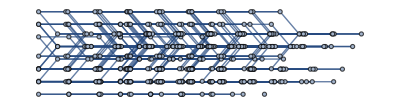

```mathematica
GraphProduct@@RandomGraph[{8,5},3]
```

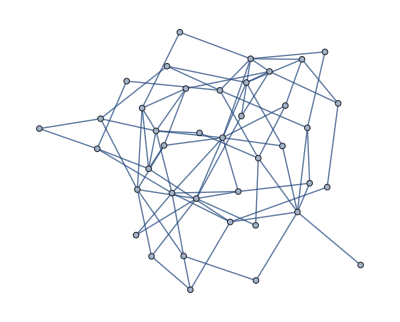
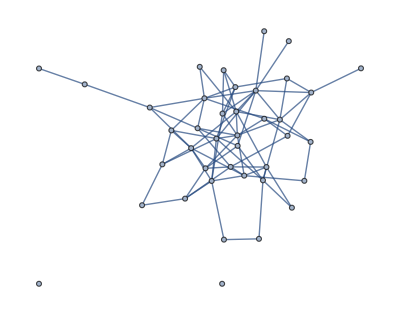
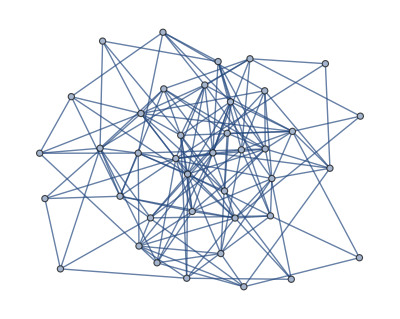
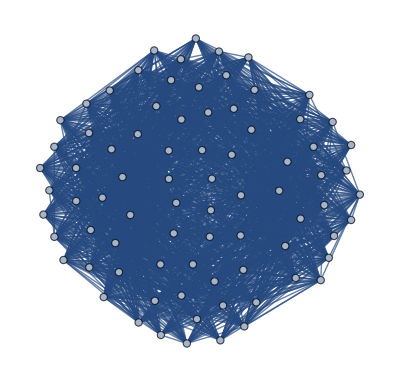
{{-Graphics-,-Graphics-},-Graphics-,-Graphics-,-Graphics-}

```mathematica
{#,GraphSum[First@#,Last@#],GraphUnion[First@#,Last@#],GraphJoin[First@#,Last@#]}&@RandomGraph[{40,80},2]
```

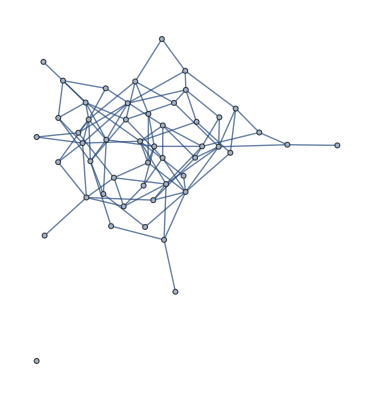
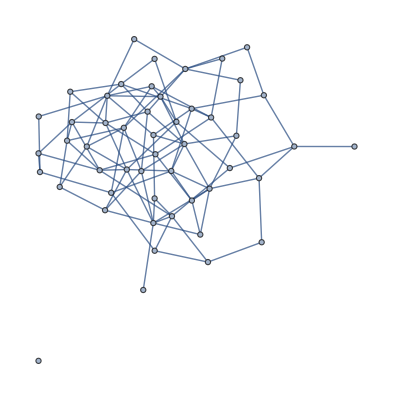
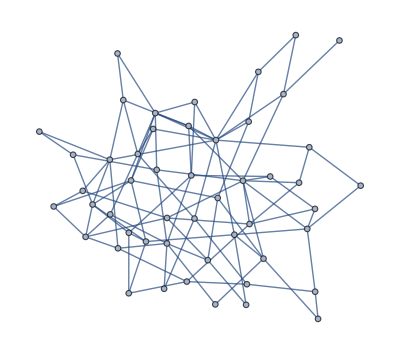

```mathematica
RandomGraph[{50,100},3]
```

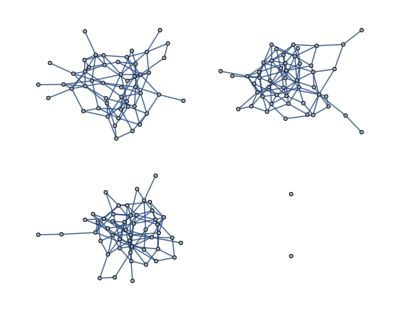

```mathematica
GraphDisjointUnion@@RandomGraph[{50,100},3]
```

```mathematica
GraphSum@@RandomGraph[{50,100},3]
```

-Graphics-

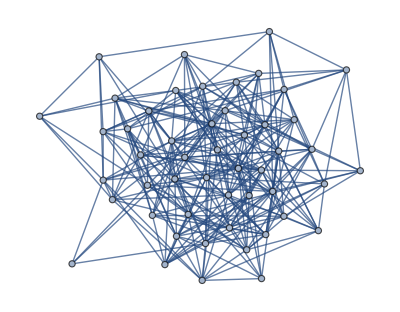

```mathematica
GraphUnion@@RandomGraph[{50,100},3]
```

```mathematica
ConnectedGraphQ[GraphSum@@RandomGraph[{50,100},3]]
```

True

```mathematica
ConnectedGraphQ[GraphUnion@@RandomGraph[{50,100},3]]
```

True

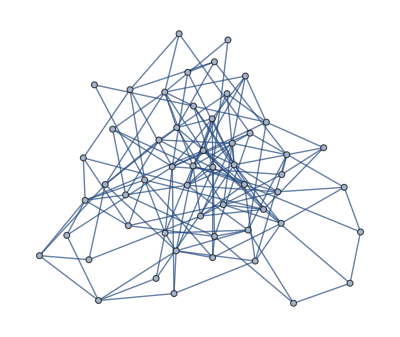

```mathematica
randomGraph=GraphUnion@RandomGraph[{54,148}]
```

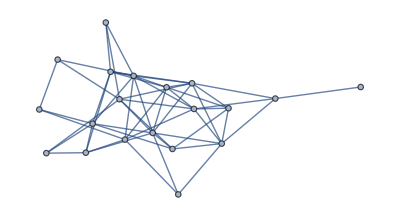
<|Graph→-Graphics-,VertexList→{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},EdgeList→{1<->4,1<->5,1<->13,1<->16,1<->20,2<->10,2<->11,2<->14,2<->17,2<->19,3<->12,4<->5,4<->9,4<->12,4<->13,4<->14,4<->16,5<->6,5<->12,5<->17,5<->18,5<->20,6<->7,6<->10,6<->11,6<->14,6<->15,6<->16,6<->17,6<->20,7<->8,7<->18,8<->10,8<->17,9<->14,9<->17,10<->11,10<->13,10<->14,10<->19,11<->15,11<->16,11<->20,12<->16,13<->14,13<->18,14<->16,14<->18,14<->20,15<->18,16<->18,16<->20,17<->20,18<->19}|>

```mathematica
<|"Graph"->randomGraph,"VertexList"->VertexList@randomGraph,"EdgeList"->EdgeList@randomGraph|>
```

```mathematica
Thread@GeoPosition[…]
```

{GeoPosition[{40.8792,-73.8245}],GeoPosition[{40.6955,-73.7751}],GeoPosition[{40.7775,-73.8213}],GeoPosition[{40.6218,-73.8747}],GeoPosition[{40.7582,-73.7949}],GeoPosition[{40.5175,-74.1186}],GeoPosition[{40.5835,-73.9589}],GeoPosition[{40.6567,-73.8575}],GeoPosition[{40.8056,-73.9666}],GeoPosition[{40.5321,-73.9478}],GeoPosition[{40.7514,-73.8389}],GeoPosition[{40.8664,-73.7855}],GeoPosition[{40.6805,-73.8436}],GeoPosition[{40.56,-73.9662}],GeoPosition[{40.6451,-73.9244}],GeoPosition[{40.7262,-73.9063}],GeoPosition[{40.5214,-73.8686}],GeoPosition[{40.8769,-73.8351}],GeoPosition[{40.7863,-73.8679}],GeoPosition[{40.5555,-74.1245}],GeoPosition[{40.8349,-73.8676}],GeoPosition[{40.7394,-73.7705}],GeoPosition[{40.7579,-73.7693}],GeoPosition[{40.5516,-74.0091}],GeoPosition[{40.7318,-73.7784}],GeoPosition[{40.8997,-73.899}],GeoPosition[{40.8707,-73.8201}],GeoPosition[{40.823,-73.8136}],GeoPosition[{40.6352,-74.0472}],GeoPosition[{40.5772,-74.1835}],GeoPosition[{40.5946,-73.9888}],GeoPosition[{40.5917,-74.0614}],GeoPosition[{40.7852,-73.9444}],GeoPosition[{40.7602,-73.9537}],GeoPosition[{40.7782,-73.8455}],GeoPosition[{40.8294,-73.8682}],GeoPosition[{40.5829,-73.8758}],GeoPosition[{40.7588,-73.9146}],GeoPosition[{40.8104,-73.8847}],GeoPosition[{40.6725,-73.9655}],GeoPosition[{40.5865,-74.1744}],GeoPosition[{40.5286,-74.0221}],GeoPosition[{40.5515,-74.0335}],GeoPosition[{40.7474,-73.8766}],GeoPosition[{40.6015,-74.1298}],GeoPosition[{40.5364,-73.9766}],GeoPosition[{40.5857,-73.7703}],GeoPosition[{40.5335,-74.1733}],GeoPosition[{40.6945,-73.7996}],GeoPosition[{40.7878,-73.7611}],GeoPosition[{40.8533,-73.7683}],GeoPosition[{40.6575,-73.8582}],GeoPosition[{40.6835,-73.8341}],GeoPosition[{40.8311,-73.9407}]}

```mathematica
AssociationThread[Range[54]->Thread@RandomGeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}],54]]
```

<|1→GeoPosition[{40.8569,-73.9327}],2→GeoPosition[{40.8226,-73.9075}],3→GeoPosition[{40.5308,-74.0761}],4→GeoPosition[{40.6325,-74.1181}],5→GeoPosition[{40.7749,-73.9728}],6→GeoPosition[{40.7528,-73.9415}],7→GeoPosition[{40.6565,-73.9898}],8→GeoPosition[{40.7325,-73.7228}],9→GeoPosition[{40.8074,-73.7987}],10→GeoPosition[{40.697,-73.8917}],11→GeoPosition[{40.7733,-73.7733}],12→GeoPosition[{40.5178,-74.1916}],13→GeoPosition[{40.6296,-73.9361}],14→GeoPosition[{40.6713,-73.9578}],15→GeoPosition[{40.5328,-73.9415}],16→GeoPosition[{40.8605,-73.9393}],17→GeoPosition[{40.7453,-73.7855}],18→GeoPosition[{40.5379,-73.8782}],19→GeoPosition[{40.7525,-74.0126}],20→GeoPosition[{40.4818,-74.202}],21→GeoPosition[{40.7286,-73.9588}],22→GeoPosition[{40.8582,-73.875}],23→GeoPosition[{40.7585,-73.7509}],24→GeoPosition[{40.4796,-74.2222}],25→GeoPosition[{40.7171,-73.9764}],26→GeoPosition[{40.8006,-73.8265}],27→GeoPosition[{40.7452,-73.8809}],28→GeoPosition[{40.5592,-74.2017}],29→GeoPosition[{40.7229,-73.8391}],30→GeoPosition[{40.5948,-73.9868}],31→GeoPosition[{40.5753,-74.1341}],32→GeoPosition[{40.7253,-73.7276}],33→GeoPosition[{40.7008,-73.9439}],34→GeoPosition[{40.5203,-74.0439}],35→GeoPosition[{40.7272,-73.8769}],36→GeoPosition[{40.4993,-73.8974}],37→GeoPosition[{40.7418,-73.724}],38→GeoPosition[{40.6325,-74.0412}],39→GeoPosition[{40.6253,-74.1324}],40→GeoPosition[{40.568,-74.1069}],41→GeoPosition[{40.7805,-73.9011}],42→GeoPosition[{40.57,-74.0177}],43→GeoPosition[{40.6618,-73.9476}],44→GeoPosition[{40.622,-74.0338}],45→GeoPosition[{40.7729,-73.8969}],46→GeoPosition[{40.7036,-73.9229}],47→GeoPosition[{40.513,-74.1851}],48→GeoPosition[{40.4942,-74.2168}],49→GeoPosition[{40.5028,-73.894}],50→GeoPosition[{40.7626,-73.8983}],51→GeoPosition[{40.5576,-73.9509}],52→GeoPosition[{40.5012,-74.2491}],53→GeoPosition[{40.6473,-73.9771}],54→GeoPosition[{40.755,-73.8542}]|>

```mathematica
Normal[AssociationThread[Range[54]->Thread@RandomGeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}],54]]]
```

{1→GeoPosition[{40.8764,-73.9215}],2→GeoPosition[{40.844,-73.8668}],3→GeoPosition[{40.6802,-73.8153}],4→GeoPosition[{40.7779,-73.777}],5→GeoPosition[{40.6028,-73.9211}],6→GeoPosition[{40.9029,-73.8774}],7→GeoPosition[{40.7895,-73.9858}],8→GeoPosition[{40.8738,-73.7869}],9→GeoPosition[{40.679,-73.885}],10→GeoPosition[{40.5009,-74.1829}],11→GeoPosition[{40.5609,-74.0079}],12→GeoPosition[{40.5104,-73.8811}],13→GeoPosition[{40.7823,-73.823}],14→GeoPosition[{40.6729,-73.7576}],15→GeoPosition[{40.6269,-74.1553}],16→GeoPosition[{40.5621,-73.8189}],17→GeoPosition[{40.5803,-73.9754}],18→GeoPosition[{40.5023,-73.9037}],19→GeoPosition[{40.5325,-74.0879}],20→GeoPosition[{40.7775,-73.9422}],21→GeoPosition[{40.7242,-73.7451}],22→GeoPosition[{40.5613,-74.1241}],23→GeoPosition[{40.5508,-73.7966}],24→GeoPosition[{40.4937,-74.172}],25→GeoPosition[{40.5467,-73.794}],26→GeoPosition[{40.7746,-73.8187}],27→GeoPosition[{40.5331,-73.9634}],28→GeoPosition[{40.8844,-73.8784}],29→GeoPosition[{40.6667,-73.8173}],30→GeoPosition[{40.707,-73.9792}],31→GeoPosition[{40.551,-73.9779}],32→GeoPosition[{40.5665,-74.2047}],33→GeoPosition[{40.5825,-74.1059}],34→GeoPosition[{40.5453,-73.8328}],35→GeoPosition[{40.534,-73.9979}],36→GeoPosition[{40.513,-73.9232}],37→GeoPosition[{40.4925,-74.203}],38→GeoPosition[{40.7708,-73.9687}],39→GeoPosition[{40.7991,-73.8488}],40→GeoPosition[{40.5981,-73.9268}],41→GeoPosition[{40.6775,-73.7559}],42→GeoPosition[{40.5959,-73.957}],43→GeoPosition[{40.8305,-73.8593}],44→GeoPosition[{40.7257,-73.7636}],45→GeoPosition[{40.5789,-73.8229}],46→GeoPosition[{40.6153,-73.8649}],47→GeoPosition[{40.5648,-73.9709}],48→GeoPosition[{40.5571,-73.9368}],49→GeoPosition[{40.7738,-73.8269}],50→GeoPosition[{40.671,-73.8264}],51→GeoPosition[{40.6334,-73.8769}],52→GeoPosition[{40.5874,-74.1279}],53→GeoPosition[{40.5484,-74.1771}],54→GeoPosition[{40.6026,-73.9344}]}

```mathematica
VertexList[randomGraph]/.(Normal[AssociationThread[Range[54]->Thread@RandomGeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}],54]]])
```

{GeoPosition[{40.7461,-73.8886}],GeoPosition[{40.5642,-73.7999}],GeoPosition[{40.6345,-73.9031}],GeoPosition[{40.8397,-73.7692}],GeoPosition[{40.5881,-73.857}],GeoPosition[{40.6615,-74.0335}],GeoPosition[{40.5542,-73.9529}],GeoPosition[{40.6222,-74.0279}],GeoPosition[{40.5741,-73.8706}],GeoPosition[{40.7736,-73.8094}],GeoPosition[{40.8443,-73.8031}],GeoPosition[{40.7548,-73.856}],GeoPosition[{40.5611,-74.1266}],GeoPosition[{40.7621,-73.7669}],GeoPosition[{40.7111,-73.8146}],GeoPosition[{40.8041,-73.8222}],GeoPosition[{40.657,-73.8203}],GeoPosition[{40.5199,-74.0045}],GeoPosition[{40.581,-74.0004}],GeoPosition[{40.6003,-73.9446}],GeoPosition[{40.767,-73.8318}],GeoPosition[{40.5433,-73.769}],GeoPosition[{40.8845,-73.9246}],GeoPosition[{40.8512,-73.9174}],GeoPosition[{40.5696,-74.1484}],GeoPosition[{40.6204,-74.0948}],GeoPosition[{40.6669,-73.7778}],GeoPosition[{40.6036,-74.1374}],GeoPosition[{40.5908,-74.0512}],GeoPosition[{40.6152,-74.025}],GeoPosition[{40.5673,-73.7852}],GeoPosition[{40.5759,-74.1123}],GeoPosition[{40.5153,-74.2102}],GeoPosition[{40.6788,-73.8764}],GeoPosition[{40.703,-73.755}],GeoPosition[{40.7541,-73.8678}],GeoPosition[{40.7652,-73.9683}],GeoPosition[{40.5928,-74.0215}],GeoPosition[{40.8144,-73.8378}],GeoPosition[{40.6856,-73.7391}],GeoPosition[{40.5529,-73.9917}],GeoPosition[{40.8316,-73.8475}],GeoPosition[{40.4991,-74.2036}],GeoPosition[{40.7181,-73.7583}],GeoPosition[{40.653,-73.8977}],GeoPosition[{40.5503,-74.2235}],GeoPosition[{40.6279,-73.9513}],GeoPosition[{40.8559,-73.9004}],GeoPosition[{40.7383,-73.9433}],GeoPosition[{40.5354,-73.8261}],GeoPosition[{40.5956,-73.9411}],GeoPosition[{40.646,-74.0235}],GeoPosition[{40.6372,-73.9965}],GeoPosition[{40.7039,-73.7498}]}

```mathematica
GeoGraphPlot[Normal[AssociationThread[Range[54]->Thread@RandomGeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}],54]]]]
```

-Graphics-

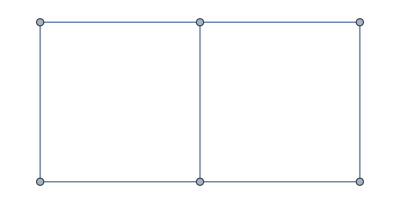

```mathematica
gridGraph=GridGraph[{2,3},AnnotationRules->{{2,3}->{"geoposition"->{Here,GeoAntipode[Here]}}}]
```

```mathematica
AnnotationValue[{gridGraph,2},"geoposition"]
```

$Failed

```mathematica
randomGeoGraph[]//Shallow
```

{GeoPosition[{«2»}],GeoPosition[{«2»}],GeoPosition[{«2»}],GeoPosition[{«2»}],GeoPosition[{«2»}],GeoPosition[{«2»}],GeoPosition[{«2»}],GeoPosition[{«2»}],GeoPosition[{«2»}],GeoPosition[{«2»}],«44»}

```mathematica
randomGeoGraph[]:=Module[{randomGraph,edgeList,vertexList,randomGeoCoordinates,geoCoordinateGraph},randomGraph=RandomGraph[{54,148}];edgeList=EdgeList[randomGraph];vertexList=VertexList[randomGraph];randomGeoCoordinates=Thread@RandomGeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}],54];geoCoordinateGraph=Graph[GraphUnion@randomGraph,AnnotationRules->Table[u->Thread[{"geoposition"}->randomGeoCoordinates[[u]]],{u,54}]]]
```

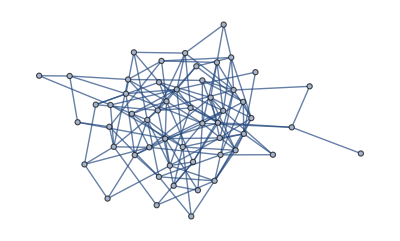

```mathematica
testGraph=randomGeoGraph[]
```

```mathematica
AnnotationValue[{testGraph,#},"geoposition"]&/@Range[54]//Short
EdgeList[testGraph]
```

{GeoPosition[{40.6476,-73.7473}],«52»,GeoPosition[{40.7132,-73.871}]}

{1<->10,1<->25,1<->27,1<->28,1<->34,1<->45,1<->53,1<->54,2<->21,2<->23,2<->46,3<->38,3<->51,4<->15,4<->16,4<->46,4<->47,5<->9,5<->14,5<->43,5<->49,6<->12,6<->19,7<->50,7<->52,8<->16,8<->26,8<->32,8<->40,8<->41,8<->43,9<->16,9<->17,9<->20,9<->51,10<->14,10<->18,10<->23,10<->29,10<->32,10<->33,10<->34,10<->35,10<->51,11<->18,11<->22,11<->23,11<->32,11<->49,11<->50,11<->51,12<->23,12<->27,12<->33,12<->36,12<->41,12<->42,12<->47,12<->52,13<->17,13<->22,13<->28,13<->47,14<->19,14<->21,14<->23,14<->26,14<->28,14<->36,14<->40,15<->25,15<->34,15<->48,16<->19,16<->24,16<->25,16<->27,16<->29,16<->32,16<->40,16<->48,17<->28,17<->43,18<->29,18<->33,18<->43,18<->50,19<->27,19<->37,19<->48,20<->34,20<->40,20<->43,20<->51,20<->54,21<->36,21<->37,21<->53,21<->54,22<->44,23<->28,23<->50,24<->26,24<->30,24<->34,24<->43,24<->45,25<->27,25<->33,25<->35,25<->39,25<->42,25<->51,26<->32,27<->33,27<->35,27<->47,27<->49,27<->50,27<->53,29<->30,29<->40,29<->51,31<->49,32<->33,33<->34,33<->36,33<->52,34<->45,34<->47,34<->50,34<->52,34<->54,35<->52,36<->53,37<->41,38<->48,38<->49,38<->54,39<->41,40<->52,42<->46,43<->50,44<->49,45<->50,47<->52,47<->53,49<->53}

```mathematica
GeoDistance[AnnotationValue[{testGraph,First[#]},"geoposition"],AnnotationValue[{testGraph,Last[#]},"geoposition"]]&/@EdgeList[testGraph]
```

```mathematica
{Quantity[32.57503746149277, "Kilometers"],Quantity[21.402915650209305, "Kilometers"],Quantity[40.601907970797804, "Kilometers"],Quantity[3.0843952757491953, "Kilometers"],Quantity[32.90729978016885, "Kilometers"],Quantity[5.4453568401589445, "Kilometers"],Quantity[11.67017924723958, "Kilometers"],Quantity[13.432978440992713, "Kilometers"],Quantity[12.020780943010868, "Kilometers"],Quantity[31.323056603353997, "Kilometers"],Quantity[21.058723801665224, "Kilometers"],Quantity[32.000485732071304, "Kilometers"],Quantity[30.543233532245196, "Kilometers"],Quantity[21.41345104899527, "Kilometers"],Quantity[18.373276632620346, "Kilometers"],Quantity[4.120800273898856, "Kilometers"],Quantity[23.11109629232218, "Kilometers"],Quantity[38.33315473395512, "Kilometers"],Quantity[38.76714039543771, "Kilometers"],Quantity[30.09418735457191, "Kilometers"],Quantity[16.18703366872883, "Kilometers"],Quantity[12.432360085422536, "Kilometers"],Quantity[15.51472732492388, "Kilometers"],Quantity[24.009878253541608, "Kilometers"],Quantity[15.505728591986493, "Kilometers"],Quantity[21.81473794248627, "Kilometers"],Quantity[28.44427028273672, "Kilometers"],Quantity[22.820552330981407, "Kilometers"],Quantity[6.123808569360403, "Kilometers"],Quantity[11.984137426148587, "Kilometers"],Quantity[2.9605981431843533, "Kilometers"],Quantity[9.70671006351847, "Kilometers"],Quantity[9.732942111669205, "Kilometers"],Quantity[25.753697634695992, "Kilometers"],Quantity[5.713855038072215, "Kilometers"],Quantity[33.94732873467085, "Kilometers"],Quantity[19.04231998684303, "Kilometers"],Quantity[13.813848543925394, "Kilometers"],Quantity[21.230291346986796, "Kilometers"],Quantity[16.511689902310113, "Kilometers"],Quantity[3.52342633982923, "Kilometers"],Quantity[12.080022593572934, "Kilometers"],Quantity[14.869804500176, "Kilometers"],Quantity[16.077287390585315, "Kilometers"],Quantity[27.78116442399735, "Kilometers"],Quantity[11.925952036170914, "Kilometers"],Quantity[7.129476257509644, "Kilometers"],Quantity[21.570023165131328, "Kilometers"],Quantity[15.819219954922163, "Kilometers"],Quantity[13.415962240923625, "Kilometers"],Quantity[10.617669082847529, "Kilometers"],Quantity[25.896918309615835, "Kilometers"],Quantity[6.50272135904814, "Kilometers"],Quantity[27.502706490281792, "Kilometers"],Quantity[9.977046807906373, "Kilometers"],Quantity[4.507996657343366, "Kilometers"],Quantity[15.896926142687752, "Kilometers"],Quantity[29.54389529652318, "Kilometers"],Quantity[27.532351562956144, "Kilometers"],Quantity[23.071393946808353, "Kilometers"],Quantity[2.8453648812515144, "Kilometers"],Quantity[1.1074709228442647, "Kilometers"],Quantity[19.913718894093815, "Kilometers"],Quantity[27.41722708179029, "Kilometers"],Quantity[9.643579890720316, "Kilometers"],Quantity[17.99370002356515, "Kilometers"],Quantity[19.682370552242322, "Kilometers"],Quantity[6.397567247386547, "Kilometers"],Quantity[18.23435566014118, "Kilometers"],Quantity[13.03773988263619, "Kilometers"],Quantity[9.267895411019452, "Kilometers"],Quantity[11.887022932902067, "Kilometers"],Quantity[9.867406890677103, "Kilometers"],Quantity[26.91166582731558, "Kilometers"],Quantity[28.288380063632054, "Kilometers"],Quantity[19.016874654638464, "Kilometers"],Quantity[43.468760834854926, "Kilometers"],Quantity[6.222305291034704, "Kilometers"],Quantity[14.316174675896233, "Kilometers"],Quantity[11.395754464002264, "Kilometers"],Quantity[21.67127336889491, "Kilometers"],Quantity[11.499202273457474, "Kilometers"],Quantity[16.88551094086264, "Kilometers"],Quantity[18.662389968974377, "Kilometers"],Quantity[30.072494566123243, "Kilometers"],Quantity[19.033641654580006, "Kilometers"],Quantity[41.965133405630496, "Kilometers"],Quantity[39.738132347748554, "Kilometers"],Quantity[29.91948809014312, "Kilometers"],Quantity[27.421763787426812, "Kilometers"],Quantity[25.589607746038343, "Kilometers"],Quantity[31.04359467977011, "Kilometers"],Quantity[52.571806539604076, "Kilometers"],Quantity[39.945300178106194, "Kilometers"],Quantity[30.413922123045413, "Kilometers"],Quantity[48.87012055588269, "Kilometers"],Quantity[1.8912100380410186, "Kilometers"],Quantity[18.01252129483121, "Kilometers"],Quantity[27.192368698320355, "Kilometers"],Quantity[11.399226243320305, "Kilometers"],Quantity[8.368324727193226, "Kilometers"],Quantity[3.5896807372576025, "Kilometers"],Quantity[12.855251276802694, "Kilometers"],Quantity[15.877880255862143, "Kilometers"],Quantity[25.60702006062133, "Kilometers"],Quantity[14.567069957813002, "Kilometers"],Quantity[27.63717075456706, "Kilometers"],Quantity[30.150716256211577, "Kilometers"],Quantity[16.342284025862345, "Kilometers"],Quantity[28.74115368781015, "Kilometers"],Quantity[15.12861020887759, "Kilometers"],Quantity[5.124871092857098, "Kilometers"],Quantity[30.060280637026302, "Kilometers"],Quantity[18.198838262708808, "Kilometers"],Quantity[12.184043866498797, "Kilometers"],Quantity[9.766877548083274, "Kilometers"],Quantity[17.699780356639515, "Kilometers"],Quantity[24.4445863938735, "Kilometers"],Quantity[10.316978312655662, "Kilometers"],Quantity[12.181359374981868, "Kilometers"],Quantity[12.706423615084779, "Kilometers"],Quantity[19.825273588127562, "Kilometers"],Quantity[20.017438911704634, "Kilometers"],Quantity[20.653963599175576, "Kilometers"],Quantity[6.577271509725978, "Kilometers"],Quantity[5.650018737443042, "Kilometers"],Quantity[21.98082598318634, "Kilometers"],Quantity[22.04155673763946, "Kilometers"],Quantity[18.616845208474285, "Kilometers"],Quantity[20.75576875760028, "Kilometers"],Quantity[26.960299144905342, "Kilometers"],Quantity[33.67534609554485, "Kilometers"],Quantity[33.94680101136436, "Kilometers"],Quantity[20.290595044771777, "Kilometers"],Quantity[15.85613343657344, "Kilometers"],Quantity[5.703251252471723, "Kilometers"],Quantity[23.633476785366913, "Kilometers"],Quantity[16.817538177251393, "Kilometers"],Quantity[47.59543675122876, "Kilometers"],Quantity[40.48315725772478, "Kilometers"],Quantity[7.597542698405171, "Kilometers"],Quantity[11.119034561217713, "Kilometers"],Quantity[4.513834284917966, "Kilometers"],Quantity[11.729123903974008, "Kilometers"],Quantity[26.253951554976318, "Kilometers"],Quantity[26.31596972514217, "Kilometers"],Quantity[15.351222602706548, "Kilometers"],Quantity[11.917439954514403, "Kilometers"]}
```

```mathematica
randomGeoGraph[{vertices_,edges_}]:=Module[{randomGraph,geoCoordinateGraph,geoGeoPositions},randomGraph=RandomGraph[{vertices,edges}];geoCoordinateGraph=Fold[Annotate[{#1,#2},"GeoPosition"->RandomGeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]]]&,randomGraph,VertexList[randomGraph]];GraphSum@Fold[Annotate[{#1,#2},EdgeWeight->GeoDistance[AnnotationValue[{geoCoordinateGraph,First@#2},"GeoPosition"],AnnotationValue[{geoCoordinateGraph,Last@#2},"GeoPosition"]]]&,geoCoordinateGraph,EdgeList[geoCoordinateGraph]]]
```

```mathematica
ReplaceAt[EdgeList[randomGeoGraph[{54,148}]],u_<->v_:>DirectedEdge[u,v],List/@RandomInteger[54,27]]
```

```mathematica
randomGeoGraph[]//InputForm//Short[#,9]&
```

Graph[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, 51, 52, 53, 54}, <<1>>, {AnnotationRules -> {38 -> {"GeoPosition" -> GeoPosition[{40.53514961102147, -74.08670872352168}]}, 6 -> {"GeoPosition" -> GeoPosition[{40.76455829433403, -73.96159103412259}]}, 23 -> {"GeoPosition" -> GeoPosition[{40.83112536176702, -73.80212839522238}]}, 1 -> {"GeoPosition" -> GeoPosition[{40.827337035838376, -73.91858844619394}]}, 2 -> {"GeoPosition" -> GeoPosition[{40.64843747271273, -73.97379160674103}]}, 21 -> {"GeoPosition" -> GeoPosition[{40.73269847029908, <<1>>}]}, <<45>>, 16 -> {"GeoPosition" -> GeoPosition[{40.85401855602561, -73.75665322810488}]}, 15 -> {"GeoPosition" -> GeoPosition[{40.50018966312787, -74.25382913808265}]}, 33 -> {"GeoPosition" -> GeoPosition[{40.75059226865847, -73.90302600278272}]}}, EdgeWeight -> <<1>>}]

```mathematica
randomMixedGeoGraph[{vertices_,edges_},mixedAmount_]:=Module[{randomGraph,randomMixedGraph,geoCoordinateGraph,geoGeoPositions},randomGraph=RandomGraph[{vertices,edges}];randomMixedGraph=Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,randomGraph,RandomSample[EdgeList[randomGraph],mixedAmount]];geoCoordinateGraph=Fold[Annotate[{#1,#2},"GeoPosition"->RandomGeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]]]&,randomMixedGraph,VertexList[randomMixedGraph]];Fold[Annotate[{#1,#2},EdgeWeight->GeoDistance[AnnotationValue[{geoCoordinateGraph,First@#2},"GeoPosition"],AnnotationValue[{geoCoordinateGraph,Last@#2},"GeoPosition"]]]&,geoCoordinateGraph,EdgeList[geoCoordinateGraph]]]
```

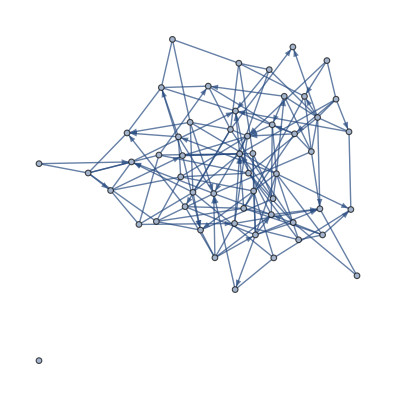

```mathematica
TimeConstrained[randomMixedGeoGraph[{54,148},60],2]
```

```mathematica
GraphJoin@@ConnectedGraphComponents@%142
```

-Graphics-

```mathematica
randomMixedGeoGraph[{54,148},60]//InputForm
```

Graph[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 
 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, 51, 52, 53, 54}, {DirectedEdge[1, 44], DirectedEdge[1, 10], DirectedEdge[1, 40], 
  DirectedEdge[2, 5], DirectedEdge[4, 11], DirectedEdge[4, 31], DirectedEdge[5, 18], DirectedEdge[6, 54], DirectedEdge[6, 9], 
  DirectedEdge[7, 51], DirectedEdge[8, 31], DirectedEdge[8, 45], DirectedEdge[8, 43], DirectedEdge[9, 53], DirectedEdge[10, 19], 
  DirectedEdge[11, 22], DirectedEdge[11, 52], DirectedEdge[12, 15], DirectedEdge[14, 15], DirectedEdge[15, 43], DirectedEdge[16, 33], 
  DirectedEdge[18, 33], DirectedEdge[19, 41], DirectedEdge[19, 21], DirectedEdge[19, 44], DirectedEdge[19, 25], DirectedEdge[20, 51], 
  DirectedEdge[20, 53], DirectedEdge[20, 49], DirectedEdge[20, 36], DirectedEdge[22, 50], DirectedEdge[22, 36], DirectedEdge[23, 51], 
  DirectedEdge[23, 38], DirectedEdge[24, 54], DirectedEdge[25, 33], DirectedEdge[25, 32], DirectedEdge[26, 46], DirectedEdge[27, 42], 
  DirectedEdge[27, 50], DirectedEdge[28, 51], DirectedEdge[29, 54], DirectedEdge[30, 40], DirectedEdge[30, 41], DirectedEdge[30, 46], 
  DirectedEdge[31, 46], DirectedEdge[31, 32], DirectedEdge[31, 37], DirectedEdge[33, 37], DirectedEdge[35, 50], DirectedEdge[36, 52], 
  DirectedEdge[41, 54], DirectedEdge[42, 51], DirectedEdge[43, 53], DirectedEdge[45, 54], DirectedEdge[45, 48], DirectedEdge[45, 50], 
  DirectedEdge[46, 51], DirectedEdge[48, 50], DirectedEdge[50, 52], UndirectedEdge[1, 2], UndirectedEdge[1, 12], UndirectedEdge[1, 17], 
  UndirectedEdge[1, 21], UndirectedEdge[2, 19], UndirectedEdge[2, 23], UndirectedEdge[2, 29], UndirectedEdge[3, 12], UndirectedEdge[3, 31], 
  UndirectedEdge[3, 43], UndirectedEdge[4, 26], UndirectedEdge[4, 30], UndirectedEdge[4, 33], UndirectedEdge[4, 54], UndirectedEdge[5, 47], 
  UndirectedEdge[6, 17], UndirectedEdge[6, 34], UndirectedEdge[6, 49], UndirectedEdge[7, 27], UndirectedEdge[7, 33], UndirectedEdge[7, 46], 
  UndirectedEdge[8, 10], UndirectedEdge[8, 25], UndirectedEdge[8, 34], UndirectedEdge[8, 44], UndirectedEdge[9, 27], UndirectedEdge[9, 30], 
  UndirectedEdge[10, 17], UndirectedEdge[10, 41], UndirectedEdge[10, 54], UndirectedEdge[11, 30], UndirectedEdge[12, 14], 
  UndirectedEdge[12, 26], UndirectedEdge[12, 43], UndirectedEdge[14, 19], UndirectedEdge[14, 22], UndirectedEdge[14, 32], 
  UndirectedEdge[15, 17], UndirectedEdge[15, 18], UndirectedEdge[15, 30], UndirectedEdge[16, 42], UndirectedEdge[17, 23], 
  UndirectedEdge[17, 41], UndirectedEdge[18, 30], UndirectedEdge[18, 35], UndirectedEdge[18, 40], UndirectedEdge[18, 44], 
  UndirectedEdge[18, 48], UndirectedEdge[20, 28], UndirectedEdge[21, 29], UndirectedEdge[21, 47], UndirectedEdge[22, 34], 
  UndirectedEdge[23, 34], UndirectedEdge[23, 47], UndirectedEdge[23, 53], UndirectedEdge[24, 42], UndirectedEdge[24, 44], 
  UndirectedEdge[25, 50], UndirectedEdge[26, 35], UndirectedEdge[28, 38], UndirectedEdge[28, 45], UndirectedEdge[30, 39], 
  UndirectedEdge[30, 52], UndirectedEdge[32, 46], UndirectedEdge[33, 39], UndirectedEdge[33, 42], UndirectedEdge[33, 47], 
  UndirectedEdge[35, 38], UndirectedEdge[35, 52], UndirectedEdge[36, 41], UndirectedEdge[36, 46], UndirectedEdge[36, 48], 
  UndirectedEdge[36, 53], UndirectedEdge[37, 42], UndirectedEdge[37, 43], UndirectedEdge[37, 53], UndirectedEdge[38, 44], 
  UndirectedEdge[38, 50], UndirectedEdge[40, 43], UndirectedEdge[40, 44], UndirectedEdge[40, 46], UndirectedEdge[40, 50], 
  UndirectedEdge[40, 53], UndirectedEdge[42, 43], UndirectedEdge[42, 53], UndirectedEdge[45, 46], UndirectedEdge[45, 53], 
  UndirectedEdge[49, 53]}]